```mathematica
SetDirectory[$UserDocumentsDirectory]
SetDirectory[".\\Research\\C-C++Code\\FuzzyPriorwEpochs\\FuzzyPriorwEpochs\\Debug"]
```

D:\Documents

D:\Documents\Research\C-C++Code\FuzzyPriorwEpochs\FuzzyPriorwEpochs\Debug

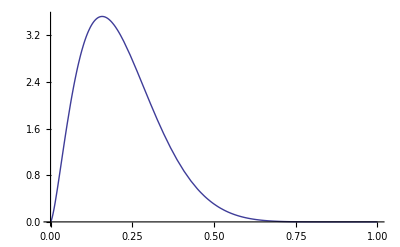

```mathematica
Plot[(PDF[BetaDistribution[2.5,9],#])&[t], {t,0,1}]
Export["FxnGen1.dat", Table[{N@t,N[(PDF[BetaDistribution[2.5,9],#])&[t]]},{t,0,1,(999)^-1}], "Table"];
```

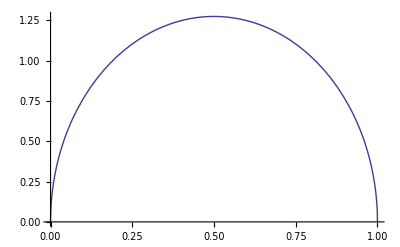

```mathematica
Plot[(PDF[BetaDistribution[1.5,1.5],#])&[t], {t,0,1}]
Export["FxnGen2.dat", Table[{N@t,N[(PDF[BetaDistribution[1.5,1.5],#])&[t]]},{t,0,1,(999)^-1}], "Table"];
```

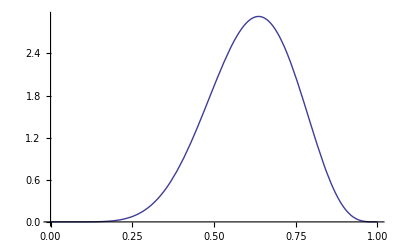

```mathematica
Plot[(PDF[BetaDistribution[8,5],#])&[t], {t,0,1}]
Export["FxnGen.dat", Table[{N@t,N[(PDF[BetaDistribution[8,5],#])&[t]]},{t,0,1,(999)^-1}], "Table"];
```

```mathematica
Directory[]
```

D:\Documents